# The Breathless Line

Reviewed by Pavel Hajek.

Can a family of shortest paths spread across a graph produce a line with no breadth? On the square grid, the normalized occupation measure converges to uniform length on a straight segment, though the union of the paths still fills a square. We prove this and compare the finite measurements to the formula.

```mathematica
Needs[ "WolframInstitute`InfraGeometry`" ]
```

## A probability measure on a segment

Let a,b be distinct vertices of a finite connected unweighted graph. Suppose there are N shortest paths between them, each of length L. If c_E(e) counts these paths through edge e, then

∑_e c_E(e)==NL.

Choose a path uniformly, then choose one of its edges uniformly. The probability of observing edge e is

p_E(e)==(c_E(e))/NL.

The occupation probability c_E(e)/N has total mass L; dividing by L makes a probability distribution over locations. InfraMeasurement supplies c_E through "EdgeDensity", without enumerating the paths.

Choose an embedding and align the endpoints to (0,0) and (1,0) using translation, rotation and uniform rescaling. Place the mass of each edge at its midpoint x(e):

μ==∑_e p_E(e)δ_(x(e)).

This is the normalization used across scales: endpoint separation and total mass are both one. The graph determines the paths and weights; the embedding determines their positions.

## The square grid

Take the grid {0,…,n}^2 with endpoints (0,0) and (n,n). Every shortest path has 2n steps, with n horizontal and n vertical steps. There are Binomial[2n, n] such paths. The aligned coordinates are

φ_n(i,j)==((i+j)/(2n),(j-i)/(2n)).

The panels show n==8,16,32 with endpoints fixed. Thickness records relative occupation within each panel. Every grid edge lies on some shortest path, so the narrowing reflects changing weights rather than shrinking support. The dashed orange lines enclose a strip of half-width 2 √((4n-1)/(48 n^2)). The second-moment computation below shows that this strip contains at least three quarters of the occupation mass at every n. Its width shrinks while the gray boundary of the support stays fixed.

```mathematica
GraphicsRow[ Table[
  With[
    { coordinates = Map[ point |-> { Total[ point ], point[[ 2 ]] - point[[ 1 ]] } / ( 2 n ),
        Tuples[ Range[ 0, n ], 2 ] ] },
    { g = GridGraph[ { n + 1, n + 1 }, VertexCoordinates -> coordinates,
        Sequence @@ InfraSubstrateStyle[ "Large" ] ] },
    { halfWidth = 2 Sqrt[ ( 4 n - 1 ) / ( 48 n^2 ) ] },
    Labeled[
      InfraSubstrateHighlight[ g, {
        InfraSegment[ 1, ( n + 1 )^2 ] -> StandardBlue,
        { 1, ( n + 1 )^2 } -> StandardBlue },
        Epilog -> {
          StandardGray, Line[ { { 0, 0 }, { 1/2, -1/2 }, { 1, 0 }, { 1/2, 1/2 }, { 0, 0 } } ],
          StandardOrange, Dashed,
          Line[ { { 0, -halfWidth }, { 1, -halfWidth } } ],
          Line[ { { 0, halfWidth }, { 1, halfWidth } } ] },
        PlotRange -> { { 0, 1 }, { -1/2, 1/2 } }, "ThicknessRange" -> { 0.1, 5 } ],
      Row[ { "n = ", n, ", strip mass at least 3/4" } ] ] ],
  { n, { 8, 16, 32 } } ], ImageSize -> 1000 ]
```

-Graphics-

## Why the breadth vanishes

Choose one of the paths uniformly and write S_k for its number of vertical steps minus horizontal steps after k steps. The vertical-step count is hypergeometric, because the n vertical steps occupy a uniformly chosen subset of the 2n positions. Consequently,

E S_k==0,    E S_k^2==(k(2n-k))/(2n-1).

Let ξ_(k+1)==S_(k+1)-S_k∈{-1,1}. Given S_k, the mean next increment is -S_k/(2n-k), so E(S_k ξ_(k+1))==-k/(2n-1). The midpoint of edge k+1 has coordinates

X==(k+1/2)/(2n),    Y==(S_k+ξ_(k+1)/2)/(2n).

Uniform edge choice makes k uniform on {0,…,2n-1}. The second moment average is

E Y^2==1/(2n)∑_(k==0)^(2n-1) (k(2n-k-1)/(2n-1)+1/4)/(4 n^2)==(4n-1)/(48 n^2).

Chebyshev's inequality gives

Pr(|Y|>δ)≤(4n-1)/(48 n^2 δ^2)<1/(12n δ^2).

For each fixed δ>0, this bound tends to zero. Taking δ==2 √(E Y^2) instead gives the three-quarter mass guarantee for the shrinking strips in the figure. For continuous f, uniform continuity on the fixed aligned square then gives Ef(X,Y)-Ef(X,0)→0. The second expectation is a midpoint Riemann sum. Therefore μ_n converges weakly to uniform length on the segment:

∫fⅆ μ_n⟶∫_0^1 f(t,0)ⅆt

for every bounded continuous f. The unscaled transverse width grows like √n lattice spacings, while its width relative to endpoint separation decreases like n^(-1/2).

## Measuring the limit

For a point (X,Y) sampled from μ, define its width and longitudinal discrepancy by

w==√(E Y^2),    D==sup_t Abs[Pr(X≤t)-U(t)],

where U is the distribution function of the uniform law on [0,1]. The square-grid formulas are

w_n==√((4n-1)/(48 n^2)),    D_n==1/(4n).

The second formula follows from the largest discrepancy at a jump of the midpoint distribution. The helper below computes both quantities from edge densities and the graph's current embedding.

```mathematica
lineReadouts[ g_Graph, a_, b_ ] :=
  With[
    { density = InfraMeasurement[ g, InfraSegment[ a, b ], "EdgeDensity" ],
      coordinates = AssociationThread[ VertexList[ g ], GraphEmbedding[ g ] ] },
    { masses = Values[ density ] / Total[ density ], direction = coordinates[ b ] - coordinates[ a ] },
    { midpoints = Map[
        edge |-> { direction, Cross[ direction ] } .
          ( Mean[ Lookup[ coordinates, List @@ edge ] ] - coordinates[ a ] ) / ( direction . direction ),
        Keys[ density ] ] },
    { order = Ordering[ midpoints[[ All, 1 ]] ] },
    { cumulative = Accumulate[ masses[[ order ]] ], positions = Clip[ midpoints[[ order, 1 ]], { 0, 1 } ] },
    { Sqrt[ masses . midpoints[[ All, 2 ]]^2 ],
      Max[ Abs[ cumulative - positions ], Abs[ cumulative - masses[[ order ]] - positions ] ] } ]
```

The orange points are measured from the graphs; the blue curves are the exact formulas. Both plots use the same endpoint and mass normalization as the pictures.

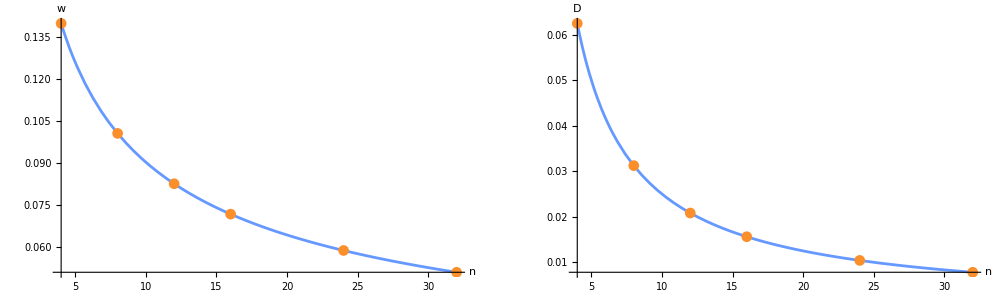

```mathematica
With[
  { readouts = Table[
      With[
        { g = GridGraph[ { n + 1, n + 1 }, VertexCoordinates -> Tuples[ Range[ 0, n ], 2 ] ] },
        Prepend[ lineReadouts[ g, 1, ( n + 1 )^2 ], n ] ],
      { n, { 4, 8, 12, 16, 24, 32 } } ] },
  GraphicsRow[ {
    Show[
      Plot[ Sqrt[ ( 4 n - 1 ) / ( 48 n^2 ) ], { n, 4, 32 },
        PlotStyle -> StandardBlue, AxesLabel -> { "n", "w" } ],
      ListPlot[ readouts[[ All, { 1, 2 } ]], PlotStyle -> StandardOrange, PlotMarkers -> Automatic ] ],
    Show[
      Plot[ 1 / ( 4 n ), { n, 4, 32 }, PlotStyle -> StandardBlue, AxesLabel -> { "n", "D" } ],
      ListPlot[ readouts[[ All, { 1, 3 } ]], PlotStyle -> StandardOrange, PlotMarkers -> Automatic ] ] },
    ImageSize -> 1000 ] ]
```

## Beyond the grid

The columns below are square, triangular and hexagonal tilings and an irregular mesh. The rows show medium and large substrates in their inherited coordinates, with endpoints aligned to (0,0) and (1,0). The blue occupation is compared with the dashed straight chord. On the shell at half the graph radius, choose its first vertex and then the vertex with the largest number of shortest paths to it. This selection rule applies uniformly across substrates.

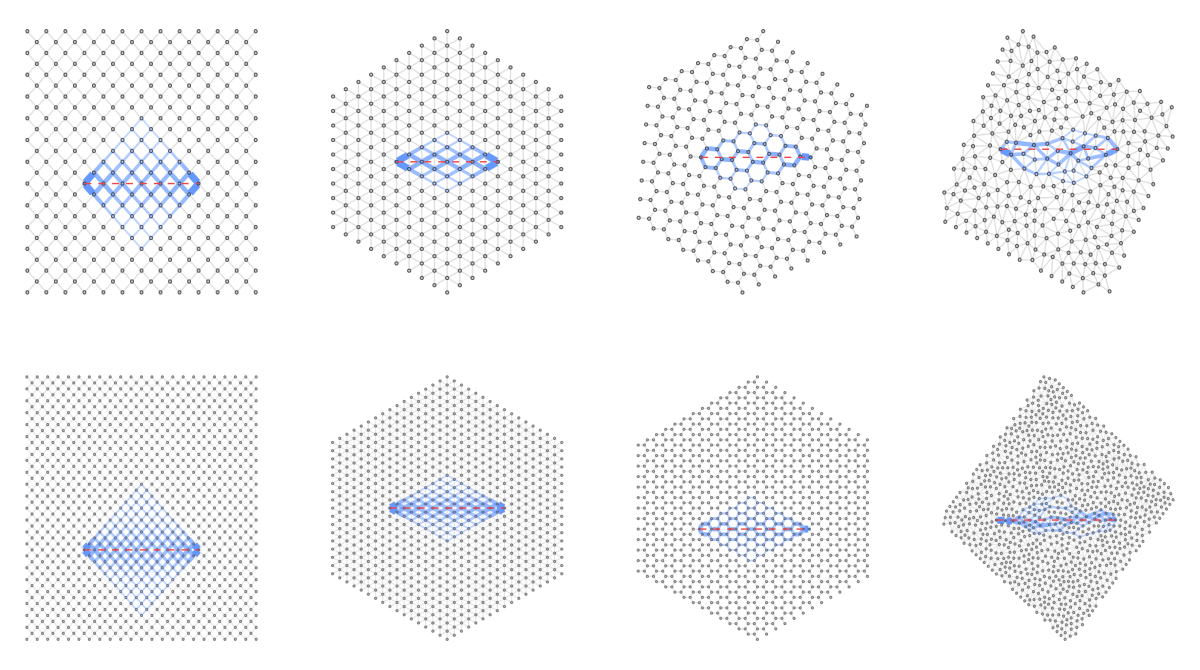

```mathematica
lineSubstrates = Table[
  With[
    { g = BlockRandom[ InfraSubstrate[ name, size, "KeepCoordinates" -> True ], RandomSeeding -> 2 ] },
    { centre = First @ GraphCenter[ g ], r = Floor[ GraphRadius[ g ] / 2 ] },
    { shell = Keys @ InfraMeasurement[ g, InfraShell[ centre, r ], "VertexDensity" ] },
    { a = First[ shell ] },
    { b = First @ MaximalBy[ shell, v |-> InfraMeasurement[ g, InfraSegment[ a, v ], "Cardinality" ] ] },
    <| "Graph" -> g, "Endpoints" -> { a, b }, "Radius" -> r, "Shell" -> shell |> ],
  { size, { "Small", "Medium", "Large" } },
  { name, { "SquareTilingGraph", "TriangularTilingGraph", "HexagonalTilingGraph", "SquareMeshGraph" } } ];
GraphicsGrid[
  Map[
    data |-> With[
      { g = data[ "Graph" ], a = data[ "Endpoints" ][[ 1 ]], b = data[ "Endpoints" ][[ 2 ]] },
      { coordinates = AssociationThread[ VertexList[ g ], GraphEmbedding[ g ] ] },
      { direction = coordinates[ b ] - coordinates[ a ] },
      { aligned = Map[ point |-> { direction, Cross[ direction ] } .
          ( point - coordinates[ a ] ) / ( direction . direction ), GraphEmbedding[ g ] ] },
      InfraSubstrateHighlight[ Graph[ g, VertexCoordinates -> aligned ], {
        InfraSegment[ a, b ] -> StandardBlue, { a, b } -> StandardBlue },
        Epilog -> { StandardRed, Dashed, Line[ { { 0, 0 }, { 1, 0 } } ] } ,
        "ThicknessRange" -> { 1.25, 5 } ] ],
    Rest[ lineSubstrates ], { 2 } ],
  ImageSize -> 1200 ]
```

Width and longitudinal discrepancy measurements compare the three sizes in each family. The horizontal axis is the shell radius used to choose the endpoints.

```mathematica
With[
  { readouts = Map[
      data |-> Prepend[ lineReadouts[ data[ "Graph" ], Sequence @@ data[ "Endpoints" ] ], data[ "Radius" ] ],
      Transpose[ lineSubstrates ], { 2 } ] },
  GraphicsRow[ {
    ListLinePlot[ readouts[[ All, All, { 1, 2 } ]], PlotRange -> All, PlotMarkers -> Automatic,
      AxesLabel -> { "r", "w" }, PlotLegends -> { "square", "triangular", "hexagonal", "mesh" } ],
    ListLinePlot[ readouts[[ All, All, { 1, 3 } ]], PlotRange -> All, PlotMarkers -> Automatic,
      AxesLabel -> { "r", "D" }, PlotLegends -> { "square", "triangular", "hexagonal", "mesh" } ] },
    ImageSize -> 1000 ] ]
```

-Graphics-

The width decreases on these meshes, while the longitudinal discrepancy first decreases then rises. The meshes are separate discretizations, so endpoints can shift with resolution. These finite measurements test the selection procedure but do not establish a limit for fixed endpoints. For a nested sequence, one could barycentrically subdivide a fixed triangulated square, retain its inherited coordinates and the same two corners, then ask whether both w_n and D_n tend to zero. Refinement alone leaves this unsettled when every new edge still carries unit graph cost.

## Triangles on different substrates

The top row shows large square, cube and sphere meshes; the bottom row shows a square torus, Sierpinski triangle and binary tree. Choose two far-apart vertices using successive graph-distance searches, then a third vertex as far as possible from the closer endpoint. Three colors display their shortest-path families in the graph's native layout. No coordinate alignment enters this construction. On a tree, the three sides share branches, so a graph triangle need not resemble a Euclidean triangle.

```mathematica
GraphicsGrid[
  Partition[
    Table[
      With[
        { g = BlockRandom[ InfraSubstrate[ specification[[ 1 ]], "Large" ], RandomSeeding -> 2 ] },
        { vertices = VertexList[ g ], distances = GraphDistanceMatrix[ g ] },
        { firstIndex = First @ Ordering[ distances[[ 1 ]], -1 ] },
        { secondIndex = First @ Ordering[ distances[[ firstIndex ]], -1 ] },
        { thirdIndex = First @ Ordering[
            Min /@ Transpose[ distances[[ { firstIndex, secondIndex } ]] ], -1 ] },
        { a = vertices[[ firstIndex ]], b = vertices[[ secondIndex ]], third = vertices[[ thirdIndex ]] },
        Labeled[
          InfraSubstrateHighlight[ g, {
            InfraSegment[ a, b ] -> StandardBlue,
            InfraSegment[ b, third ] -> StandardOrange,
            InfraSegment[ third, a ] -> StandardRed,
            { a, b, third } -> StandardBlue } ,
            "ThicknessRange" -> { 1.25, 5 } ],
          specification[[ 2 ]] ] ],
      { specification, {
          { "SquareMeshGraph", "square mesh" }, { "CubeMeshGraph", "cube mesh" },
          { "SphereMeshGraph", "sphere mesh" }, { "SquareTorusGraph", "square torus" },
          { "SierpinskiTriangleGraph", "Sierpinski triangle" }, { "BinaryTreeGraph", "binary tree" } } } ],
    3 ],
  ImageSize -> 1200 ]
```

-Graphics-

If three normalized side measures converge in a common ambient space, their equal mixture converges to the mixture of the three limits. When those limits are uniform measures on straight segments, each side has mass 1/3; this equals normalized perimeter length only when the side lengths match.

The grid example shows that occupation can concentrate on Euclidean segments without making graph distances Euclidean. The Metric Tensor examines this remaining anisotropy.

Related Guides

EuclideanInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/EuclideanInfrageometry

Related Tech Notes

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/BreathlessLineTutorial

### Keywords

line

triangle

shortest paths

occupation probability

weak convergence

square grid

mesh

scaling limit